```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/peeter/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
$Assumptions = a ∈ Reals && a > 0;
i = Integrate[Exp[I a Sin[x]], {x, 0, 2 Pi}]
i// TraditionalForm
```

2 π BesselJ[0,a]

2 π 0a

```mathematica
BesselJ[0,-a]
```

BesselJ[0,a]

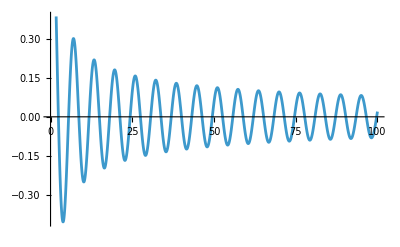

```mathematica
j0Fig4 = Plot[BesselJ[0,a], {a, 0, 100}]
```

```mathematica
ClearAll[i2, r, k, e]
$Assumptions = r ∈ Reals && r > 0 && k ∈ Reals && e ∈ Reals;
i2 = -(1/(2 Pi))Integrate[p BesselJ[0,p r]/(p^2 - (k + I e)^2),{p, 0, Infinity}]
i2 // TraditionalForm
```

ConditionalExpression[-BesselK[0,r/(√(1/(e-ⅈ k)^2))]/(2 π), e≠0]

ConditionalExpression[-(0r/(√(1/(e-ⅈ k)^2)))/(2 π), e≠0]

```mathematica
$Assumptions = r ∈ Reals && r > 0 && k ∈ Reals;
r √((-ⅈ k)^2)//FullSimplify
```

ⅈ r Abs[k]

```mathematica
peeters`exportForLatex["j0Fig4",j0Fig4]
```

{j0Fig4.eps,j0Fig4pn.png}

```mathematica
With[{k = 7},
1/(1/Sqrt[0.0000001 -I k ]^2)//N]
```

1.×10^-7-7. ⅈ

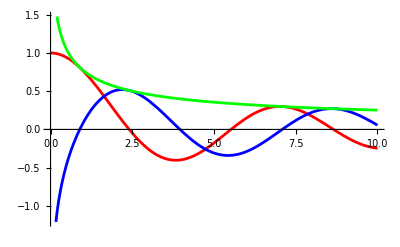

```mathematica
ClearAll[hankelPlotFig6]
hankelPlotFig6 = Plot[{
Re[HankelH1[0, x]], 
Im[HankelH1[0, x]], 
Abs[HankelH1[0, x]]
},
{x,0,10},
PlotLegends->{
MaTeX["\\mathrm{Re}\,H_0^{(1)}(x)"],
MaTeX["\\mathrm{Im}\,H_0^{(1)}(x)"],
MaTeX["\\lvert H_0^{(1)}(x) \\rvert"]
},
PlotStyle->{Red,Blue, Green}]
(*Hankel Function of the First Kind (Order 0)*)

(*Plot[Abs[HankelH1[0, x]],{x,0,10}]
Plot[Arg[HankelH1[0, x]],{x,0,10}]*)
```

```mathematica
peeters`exportForLatex["hankelPlotFig6",hankelPlotFig6]
```

{hankelPlotFig6.eps,hankelPlotFig6pn.png}